# Лабораторная работа 6. Работа с файлами.

## Задание 1.

Реализуйте самостоятельно алгоритм факторизации целых чисел методом грубой силы (перебор делителей).
Проведите исследование скорости работы.
Улучшите скорость работы алгоритма при непосредственном вызове, проведя необходимую предварительную подготовку. Вычислите результаты функции предварительно и запишите их в файл. После этого, вычислять заново нужно только те, разложения, которых нет в файле.
Проведите исследование скорости работы улучшенного алгоритма.

```mathematica
(*Разбираюсь с алгоритмом*)
(*Производится перебор всех целых чисел от 2 до квадратного корня из факторизуемого числа n и в вычислении остатка от деления n на каждое из этих чисел. Если остаток от деления на некоторое число m равен нулю,то m является делителем n. В этом случае n сокращается на m и процедура повторяется.По достижении квадратного корня из оставшегося числа и невозможности сократить его ни на одно из меньших чисел,оно объявляется простым и также приписывается к простым сомножителям исходного числа n*)
```

```mathematica
n=12234;
i=2;
While[i<Sqrt[n],If[Head[n/i]===Integer,n=n/i;Print[i],Nothing];i++]
Print[n]
```

2

3

2039

```mathematica
factorize[n_]:=Block[{i=2,list={},tempN=n},While[i<Sqrt[tempN],If[Head[tempN/i]===Integer,list=Append[list,i];tempN=tempN/i,Nothing];i++];list=Append[list,tempN];Return[list]]
```

```mathematica
factorize[15556]
```

{2,7778}

```mathematica
Timing[factorize[1234563567]]
Timing[factorize[12345635645]]
Timing[factorize[123456356456]]
Timing[factorize[1234563564561]]
```

{0.046875,{3,61,6746249}}

{0.109375,{5,7,3881,90887}}

{0.015625,{2,4,23,61,137,80287}}

{27.3906,{3,59,6974935393}}

```mathematica
(*Разбираюсь*)
SetDirectory[NotebookDirectory[]];
(*Sets the current working directory to the directory of the current evaluation notebook.*)
```

```mathematica
(*Gives the directory of the current evaluation notebook.*)
NotebookDirectory[]
```

D:\wolfram-tasks\

```mathematica
testl={1,2,3,4}
```

{1,2,3,4}

```mathematica
Export["test.txt",testl]
(*Exports data to a file, converting it to the format corresponding to the file extension*)
```

test.txt

```mathematica
templ=Import["test.txt"]
```

1
2
3
4

```mathematica
templ//Head
```

String

```mathematica
StringSplit[templ]
```

{1,2,3,4}

```mathematica
(*Как строку*)
Export["test.txt",testl,"String"]
```

test.txt

```mathematica
templ=Import["test.txt"]
templ//Head
```

{1, 2, 3, 4}

String

```mathematica
(*Обратно в выражение*)
ToExpression@templ
%//Head
```

{1,2,3,4}

List

```mathematica
Export["test.dat",testl]
```

test.dat

```mathematica
Import["test.dat"]//Flatten
```

{1,2,3,4}

```mathematica
(*Допустим, заранее записал в файл диапазон*)
writeFactorization[n1_,n2_]:=Block[{lst={}},For[i=n1,i<=n2,i++,lst=Insert[lst,Insert[factorize[i],i,1],-1]];Export["factorization.csv",lst]]
writeFactorization[2,100]
```

factorization.csv

```mathematica
l={};
l=Import["factorization.csv"];
MemberQ[l[[All,1]],9]
First[Position[l[[All,1]],9]]
```

True

{8}

```mathematica
l[[8]]
```

{9,9}

```mathematica
MemberQ[{{},{},{}}]
```

```mathematica
betterFactorization[n_]:=Block[{lst={},pos,fact,tmp},lst=Import["factorization.csv"];If[MemberQ[lst[[All,1]],n],pos=First[First[Position[lst[[All,1]],n]]];Return[Delete[lst[[pos]],1]],fact=factorize[n];tmp=Insert[fact,n,1];lst=Insert[lst,tmp,-1];
Export["factorization.csv",lst];Return[fact]]]
```

```mathematica
betterFactorization[100]
```

{2,5,10}

```mathematica
Timing[betterFactorization[1234563567]]
Timing[betterFactorization[12345635645]]
Timing[betterFactorization[123456356456]]
Timing[betterFactorization[1234563564561]]
```

{0.015625,{}}

{0.03125,{}}

{0.03125,{}}

{0.015625,{}}

## Задание 2.

Реализуйте функцию, которая выводит список файлов в некоторой директории. 
1. Упорядоченный по названию файла.
2. Упорядоченный по расширению файла.
3. Упорядоченный по размеру файла.

Важно! Изучите единицы измерения размера файла в WM. Они могут вас удивить.
https://ru.wikipedia.org/wiki/%D0%9C%D0%B5%D0%B1%D0%B8%D0%B1%D0%B0%D0%B9%D1%82

```mathematica
SetDirectory[NotebookDirectory[]];
(*Sets the current working directory to the directory of the current evaluation notebook.*)
```

```mathematica
(*Gives the directory of the current evaluation notebook.*)
NotebookDirectory[]
```

D:\wolfram-tasks\

```mathematica
(*Lists all files in the current working directory.*)
files=FileNames[];
```

```mathematica
files
```

{covid_history.csv,.git,lab-1-Shpak.nb,lab-2-Shpak.nb,lab-3-Shpak.nb,lab-4-Shpak.nb,lab-5-Shpak.nb,lab-6-Shpak.nb,LC1_3gr.nb,LC2_3gr.nb,Lec5_ped.nb,lec6_3gr.nb,LR1_3gr.nb,LR2_3gr.nb,LR3_3gr.nb,LR4_3gr.nb,LR5_3gr.nb,LR6_3gr.nb,README.md,Shpak_2.nb,test.csv,test.dat,test.txt}

```mathematica
sortByName[list_]:=Sort[list]
sortByName[files]
```

{covid_history.csv,.git,lab-1-Shpak.nb,lab-2-Shpak.nb,lab-3-Shpak.nb,lab-4-Shpak.nb,lab-5-Shpak.nb,lab-6-Shpak.nb,LC1_3gr.nb,LC2_3gr.nb,Lec5_ped.nb,lec6_3gr.nb,LR1_3gr.nb,LR2_3gr.nb,LR3_3gr.nb,LR4_3gr.nb,LR5_3gr.nb,LR6_3gr.nb,README.md,Shpak_2.nb,test.csv,test.dat,test.txt}

```mathematica
UnitConvert[FileSize[#],"Kibibytes"]&/@FileNames[]
UnitConvert[FileSize[#],"Bytes"]&/@FileNames[]
UnitConvert[FileSize[#],"Mebibytes"]&/@FileNames[]
```

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1259.14 KiB,UnitConvert[FileSize[.git],Kibibytes],257.96 KiB,57.1289 KiB,144.219 KiB,4787.6 KiB,1288.31 KiB,107.877 KiB,31.8779 KiB,23.2363 KiB,472.449 KiB,227.754 KiB,200.191 KiB,43.7891 KiB,142.751 KiB,89.5596 KiB,50.0859 KiB,76.1904 KiB,0.12793 KiB,52.584 KiB,0.950195 KiB,0.00976563 KiB,0.0117188 KiB}

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1.28936×10^6 B,UnitConvert[FileSize[.git],Bytes],264151. B,58500. B,147680. B,4.9025×10^6 B,1.31923×10^6 B,110466. B,32643. B,23794. B,483788. B,233220. B,204996. B,44840. B,146177. B,91709. B,51288. B,78019. B,131. B,53846. B,973. B,10. B,12. B}

FileSize::fdir: The specified path .git refers to a directory; a file path was expected.

{1.22963 MiB,UnitConvert[FileSize[.git],Mebibytes],0.251914 MiB,0.0557899 MiB,0.140839 MiB,4.67539 MiB,1.25811 MiB,0.105349 MiB,0.0311308 MiB,0.0226917 MiB,0.461376 MiB,0.222416 MiB,0.195499 MiB,0.0427628 MiB,0.139405 MiB,0.0874605 MiB,0.048912 MiB,0.0744047 MiB,0.000124931 MiB,0.0513515 MiB,0.000927925 MiB,9.53674×10^-6 MiB,0.0000114441 MiB}

## Задание 3.

Реализуйте возможность ограничения регулярности вызова функции (возьмите любую из предыдущих ЛР).
Функция должна вызываться не чаще, чем раз в 30 секунд (или любой другой интервал). Для этого стоит хранить историю времени вызовов функции в файле.

## Задание 4.

Запишите в файл своеобразную таблицу интегралов, вычисленную в WM с помощью встроенной функции.
После этого реализуйте функция, которая считает интегралы, используя ваш файл.

```mathematica
f=x^2;
```

```mathematica
Integrate[f,x]
```

x^3/3

## Задание 5.

Реализуйте функцию, для генерации текстового файла, некоторого размера.
Файл состоит из случайных (безсвязных) слов английского алфавита записанных по строкам. 
Функция принимает на вход: 
Максимальный размер строки (клоичество слов в сторке).
Максимальную длину одного слова.
Точный размер в Мегабайтах (Мебибайтах).

Обеспечьте возможность котнроля текущего статуса работы с помощью функции Monitor[].

Реализуйте возможность выбора языка слов*

Указание! Файл следует записывать построчно, используя функции для поточной записи при этом, контролируя текущий размер файла. Размер файла коррелирует с размером строки.

```mathematica
characters=CharacterRange["a","z"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
randomword[n_]:=StringJoin@RandomSample[characters,n]
```

```mathematica
randomword[10](*пример слова*)
```

lbtfzoyceu

```mathematica
StringRiffle[Table[randomword[RandomInteger[{3,10}]],RandomInteger[{5,20}]]](*строка файла*)
```

vubscjqyak pjcgkon vbpaijes wmxheul qpm lanx leij

## Задание 6.

Пусть задан текстовый файл. В нём записаны слова (одна строка файла - одно слово). Реализуйте возможность удаления повторяющихся слов в файле. 
Считывать весь файл целиком нельзя! Используйте поточное считывание\запись.

```mathematica
s=OpenRead["simple-words.txt"]
words={};
tmp=" ";
```

InputStream[…]

```mathematica
tmp=ReadLine[s];
While[tmp!=EndOfFile,If[!MemberQ[words,tmp],words=Append[words,tmp],Nothing];tmp=ReadLine[s]]
```

```mathematica
words
```

{}

```mathematica
Close@s
```

simple-words.txt

## Задание 7.

Пусть задан текстовый файл. В нём записаны слова (слова разделены запятой и пробелом). Представьте файл, хранящий те же слова, но в отсортированном виде.

```mathematica
s=OpenRead["poem.txt"]
wordsStr=ReadString[s]
Close@s
```

InputStream[…]

do, not, go, gentle, into, that, good, night, old, age, should, burn, and, rave, at, close, of, day, age, rage, against, the, dying, of, the, light, though, wise, men, at, their, end, know, dark, is, right, because, their, words, had, forked, no, lightning, they, do, not, go, gentle, into, that, good, night, good, men, the, last, wave, by, crying, how, bright, their, frail, deeds, might, have, danced, in, a, green, bay, rage, rage, against, the, dying, of, the, light

poem.txt

```mathematica
wordsStr=StringDelete[wordsStr,","]
```

do not go gentle into that good night old age should burn and rave at close of day age rage against the dying of the light though wise men at their end know dark is right because their words had forked no lightning they do not go gentle into that good night good men the last wave by crying how bright their frail deeds might have danced in a green bay rage rage against the dying of the light

```mathematica
Sort[StringSplit[wordsStr]]
```

{a,against,against,age,age,and,at,at,bay,because,bright,burn,by,close,crying,danced,dark,day,deeds,do,do,dying,dying,end,forked,frail,gentle,gentle,go,go,good,good,good,green,had,have,how,in,into,into,is,know,last,light,light,lightning,men,men,might,night,night,no,not,not,of,of,of,old,rage,rage,rage,rave,right,should,that,that,the,the,the,the,the,their,their,their,they,though,wave,wise,words}

```mathematica
Export["sorted-words.txt",Sort[StringSplit[wordsStr]]]
```

sorted-words.txt

## Задание 8.

Используя файл covid_history.csv выполните следующие задачи. 
1. Графически интерпретируйте данные, предварительно их обработав.
2. Проверьте выполнение закона Бенфорда для определённой страны или всех данных сразу. 
3. Записшите в новый файл, какая страна лидировала по количеству заболевших в каждый из дней.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
data=Import["covid_history.csv"];
```

```mathematica
data⟦All,2⟧
```

{World,557.,655.,941.,1434.,2118.,2927.,5578.,6167.,8235.,9927.,12038.,16787.,19887.,23898.,27643.,30805.,34399.,37130.,40161.,42769.,44812.,45230.,60382.,66910.,69053.,71236.,73271.,75153.,75653.,76213.,76842.,78603.,78984.,79552.,80406.,81383.,82742.,84136.,86031.,88411.,90389.,92998.,95334.,98154.,102082.,106203.,110119.,114307.,119196.,126868.,132944.,147113.,158190.,169580.,184404.,200470.,220111.,247356.,278381.,310431.,345552.,388486.,429622.,480895.,543881.,608809.,678383.,735021.,800224.,877292.,959597.,1.04241×10^6,1.12636×10^6,1.18531×10^6,1.25544×10^6,1.32926×10^6,1.39864×10^6,1.48223×10^6,1.56886×10^6,1.65419×10^6,1.72807×10^6,1.84697×10^6,1.91798×10^6,2.00168×10^6,2.08×10^6,2.17439×10^6,2.26207×10^6,2.33866×10^6,2.41487×10^6,2.49073×10^6,2.56632×10^6,2.64781×10^6,2.73108×10^6,2.81481×10^6,2.8979×10^6,2.96853×10^6,3.03937×10^6,3.11521×10^6,3.19255×10^6,3.27577×10^6,3.36456×10^6,3.44358×10^6,3.51789×10^6,3.5952×10^6,3.67489×10^6,3.76566×10^6,3.85418×10^6,3.94489×10^6,4.02906×10^6,4.10418×10^6,4.18056×10^6,4.26551×10^6,4.34988×10^6,4.44508×10^6,4.54123×10^6,4.63534×10^6,4.71333×10^6,4.80245×10^6,4.89912×10^6,5.00413×10^6,5.10996×10^6,5.21751×10^6,5.32156×10^6,5.4148×10^6,5.5027×10^6,5.59565×10^6,5.69822×10^6,5.81804×10^6,5.93954×10^6,6.07453×10^6,6.17676×10^6,6.27625×10^6,6.40066×10^6,6.51193×10^6,6.65017×10^6,6.78376×10^6,6.91365×10^6,7.02472×10^6,7.12797×10^6,7.25428×10^6,7.39102×10^6,7.52628×10^6,7.6542×10^6,7.78782×10^6,7.91993×10^6,8.04465×10^6,8.18918×10^6,8.33228×10^6,8.47516×10^6,8.65645×10^6,8.84213×10^6,8.93513×10^6,9.07694×10^6,9.24517×10^6,9.41648×10^6,9.59563×10^6,9.78871×10^6,9.96522×10^6,1.0133×10^7,1.0286×10^7,1.04693×10^7,1.06847×10^7,1.08889×10^7,1.10918×10^7,1.12815×10^7,1.14674×10^7,1.16354×10^7,1.18443×10^7,1.206×10^7,1.22838×10^7,1.25169×10^7,1.273×10^7,1.29215×10^7,1.31174×10^7,1.33379×10^7,1.35675×10^7,1.38119×10^7,1.40496×10^7,1.42851×10^7,1.44972×10^7,1.47059×10^7,1.49481×10^7,1.52239×10^7,1.55037×10^7,1.57876×10^7,1.60361×10^7,1.6249×10^7,1.64838×10^7,1.67483×10^7,1.70193×10^7,1.72996×10^7,1.75887×10^7,1.78348×10^7,1.80659×10^7,1.82714×10^7,1.85369×10^7,1.88129×10^7,1.90991×10^7,1.93823×10^7,1.9647×10^7,1.98805×10^7,2.01147×10^7,2.03799×10^7,2.06551×10^7,2.0945×10^7,2.12528×10^7,2.15006×10^7,2.17111×10^7,2.1925×10^7,2.21839×10^7,2.24619×10^7,2.27323×10^7,2.29953×10^7,2.32569×10^7,2.34605×10^7,2.36892×10^7,2.3934×10^7,2.42159×10^7,2.45028×10^7,2.47872×10^7,2.50475×10^7,2.52661×10^7,2.55316×10^7,2.57982×10^7,2.60803×10^7,2.63659×10^7,2.66671×10^7,2.69399×10^7,2.71694×10^7,2.7388×10^7,2.76339×10^7,2.79189×10^7,2.82227×10^7,2.85392×10^7,2.88272×10^7,2.90752×10^7,2.93434×10^7,2.96235×10^7,2.99287×10^7,3.02432×10^7,3.05709×10^7,3.08624×10^7,3.1118×10^7,3.13785×10^7,3.16621×10^7,3.1974×10^7,3.22946×10^7,3.2625×10^7,3.29088×10^7,3.31564×10^7,3.342×10^7,3.3702×10^7,3.40269×10^7,3.43461×10^7,3.46754×10^7,3.49719×10^7,3.52311×10^7,3.55437×10^7,3.58589×10^7,3.62089×10^7,3.65688×10^7,3.6929×10^7,3.72829×10^7,3.75706×10^7,3.78657×10^7,3.81846×10^7,3.8566×10^7,3.89746×10^7,3.93841×10^7,3.97536×10^7,4.00828×10^7,4.04613×10^7,4.08515×10^7,4.12951×10^7,4.17704×10^7,4.22667×10^7,4.27185×10^7,4.3077×10^7,4.35639×10^7,4.40322×10^7,4.45529×10^7,4.51052×10^7,4.56778×10^7,4.61472×10^7,4.65817×10^7,4.71416×10^7,4.76959×10^7,4.82023×10^7,4.8823×10^7,4.94426×10^7,5.00353×10^7,5.05214×10^7,5.10252×10^7,5.16037×10^7,5.22303×10^7,5.28749×10^7,5.35344×10^7,5.41146×10^7,5.45901×10^7,5.51198×10^7,5.57304×10^7,5.63585×10^7,5.70133×10^7,5.76861×10^7,5.82731×10^7,5.87597×10^7,5.92944×10^7,5.9887×10^7,6.05178×10^7,6.11099×10^7,6.18012×10^7,6.24035×10^7,6.28859×10^7,6.33934×10^7,6.40171×10^7,6.46639×10^7,6.5356×10^7,6.60446×10^7,6.66933×10^7,6.72298×10^7,6.77575×10^7,6.84006×10^7,6.90753×10^7,7.05783×10^7,7.12854×10^7,7.19268×10^7,7.24607×10^7,7.30039×10^7,7.36675×10^7,7.43925×10^7,7.51337×10^7,7.58575×10^7,7.6477×10^7,7.70146×10^7,7.75672×10^7,7.82328×10^7,7.89257×10^7,7.96144×10^7,8.01035×10^7,8.06188×10^7,8.103×10^7,8.15309×10^7,8.22039×10^7,8.29407×10^7,8.37683×10^7,8.43416×10^7,8.49313×10^7,8.54518×10^7,8.60108×10^7,8.67556×10^7,8.75519×10^7,8.84427×10^7,8.92674×10^7,9.00222×10^7,9.06109×10^7,9.12242×10^7,9.19289×10^7,9.26791×10^7,9.34357×10^7,9.4209×10^7,9.48612×10^7,9.53898×10^7,9.59093×10^7,9.65005×10^7,9.72015×10^7,9.78578×10^7,9.85221×10^7,9.90956×10^7,9.95573×10^7,1.00039×10^8,1.00602×10^8,1.01206×10^8,1.01816×10^8,1.02408×10^8,1.02927×10^8,1.03315×10^8,1.03759×10^8,1.04226×10^8,1.04752×10^8,1.05223×10^8,1.05759×10^8,1.06193×10^8,1.06544×10^8,1.06884×10^8,1.07292×10^8,1.07734×10^8,1.08177×10^8,1.08607×10^8,1.08987×10^8,1.09294×10^8,1.09576×10^8,1.09937×10^8,1.10325×10^8,1.10735×10^8,1.11145×10^8,1.11519×10^8,1.11837×10^8,1.12132×10^8,1.12527×10^8,1.12974×10^8,1.13427×10^8,1.13869×10^8,1.14265×10^8,1.14572×10^8,1.14878×10^8,1.15193×10^8,1.15637×10^8,1.16095×10^8,1.16544×10^8,1.16957×10^8,1.1733×10^8,1.17634×10^8,1.18051×10^8,1.18522×10^8,1.19002×10^8,1.19492×10^8,1.19945×10^8,1.20308×10^8,1.20663×10^8,1.21133×10^8,1.21683×10^8,1.2223×10^8,1.22792×10^8,1.23289×10^8,1.23724×10^8,1.24146×10^8,1.24666×10^8,1.25303×10^8,1.25955×10^8,1.26594×10^8,1.27175×10^8,1.27651×10^8,1.28112×10^8,1.28687×10^8,1.29369×10^8,1.30077×10^8,1.30715×10^8,1.31241×10^8,1.31797×10^8,1.32292×10^8,1.32899×10^8,1.33583×10^8,1.34425×10^8,1.35171×10^8,1.35835×10^8,1.36529×10^8,1.37142×10^8,1.37925×10^8,1.38746×10^8,1.39562×10^8,1.40418×10^8,1.41207×10^8,1.41889×10^8,1.42584×10^8,1.43445×10^8,1.44333×10^8,1.45235×10^8,1.46138×10^8,1.46953×10^8,1.47678×10^8,1.48361×10^8,1.49215×10^8,1.50119×10^8,1.51014×10^8,1.51896×10^8,1.5269×10^8,1.5337×10^8,1.54057×10^8,1.54859×10^8,1.55705×10^8,1.56574×10^8,1.57406×10^8,1.58192×10^8,1.58829×10^8,1.59456×10^8,1.60194×10^8,1.60954×10^8,1.61686×10^8,1.62394×10^8,1.63026×10^8,1.63571×10^8,1.64115×10^8,1.64738×10^8,1.65411×10^8,1.65692×10^8,1.66317×10^8,1.66889×10^8,1.67369×10^8,1.6782×10^8,1.68355×10^8,1.68925×10^8,1.69473×10^8,1.69978×10^8,1.70457×10^8,1.70847×10^8,1.71234×10^8,1.71695×10^8,1.72182×10^8,1.72662×10^8,1.73087×10^8,1.73484×10^8,1.73807×10^8,1.74129×10^8,1.74501×10^8,1.74919×10^8,1.75373×10^8,1.75795×10^8,1.76163×10^8,1.76466×10^8,1.76775×10^8,1.77151×10^8,1.77539×10^8,1.77935×10^8,1.78339×10^8,1.78687×10^8,1.7899×10^8,1.79287×10^8,1.79697×10^8,1.80094×10^8,1.80503×10^8,1.80921×10^8,1.81284×10^8,1.81595×10^8,1.81928×10^8,1.82309×10^8,1.82708×10^8,1.83144×10^8,1.83586×10^8,1.8396×10^8,1.84288×10^8,1.84665×10^8,1.85116×10^8,1.85581×10^8,1.86063×10^8,1.86576×10^8,1.86998×10^8,1.87368×10^8,1.87801×10^8,1.88327×10^8,1.88865×10^8,1.89441×10^8,1.90037×10^8,1.90526×10^8,1.90948×10^8,1.91435×10^8,1.91968×10^8,1.92523×10^8,1.93088×10^8,1.93816×10^8,1.94248×10^8,1.94693×10^8,1.95233×10^8,1.9584×10^8,1.9649×10^8,1.97132×10^8,1.97864×10^8,1.98381×10^8,1.98862×10^8,1.99435×10^8,2.00069×10^8,2.0075×10^8,2.01434×10^8,2.02253×10^8,2.02813×10^8,2.0328×10^8,2.03901×10^8,2.04547×10^8,2.05276×10^8,2.05983×10^8,2.06784×10^8,2.07336×10^8,2.07802×10^8,2.08468×10^8,2.0915×10^8,2.09885×10^8,2.10596×10^8,2.11382×10^8,2.11936×10^8,2.12385×10^8,2.13073×10^8,2.13761×10^8,2.14493×10^8,2.15232×10^8,2.15973×10^8,2.16532×10^8,2.16977×10^8,2.17644×10^8,2.18278×10^8,2.19004×10^8,2.19678×10^8,2.20392×10^8,2.20888×10^8,2.2133×10^8,2.21778×10^8,2.2248×10^8,2.23109×10^8,2.23756×10^8,2.24396×10^8,2.2486×10^8,2.25234×10^8,2.25821×10^8,2.26371×10^8,2.26942×10^8,2.27526×10^8,2.28148×10^8,2.28674×10^8,2.2904×10^8,2.29565×10^8,2.30052×10^8,2.30592×10^8,2.31138×10^8,2.31688×10^8,2.32066×10^8,2.32424×10^8,2.32899×10^8,2.33354×10^8,2.33844×10^8,2.34333×10^8,2.34854×10^8,2.35209×10^8,2.3552×10^8,2.35959×10^8,2.36385×10^8,2.36893×10^8,2.37354×10^8,2.3783×10^8,2.38174×10^8,2.38494×10^8,2.38872×10^8,2.39314×10^8,2.39772×10^8,2.40224×10^8,2.40684×10^8,2.41032×10^8,2.41349×10^8,2.41763×10^8,2.4221×10^8,2.42688×10^8,2.43152×10^8,2.43641×10^8,2.44013×10^8,2.44329×10^8,2.44757×10^8,2.45206×10^8,2.45726×10^8,2.4619×10^8,2.46699×10^8,2.47088×10^8,2.47434×10^8,2.47855×10^8,2.48281×10^8,2.48819×10^8,2.49343×10^8,2.49864×10^8,2.50291×10^8,2.5064×10^8,2.51118×10^8,2.51606×10^8,2.52195×10^8,2.52713×10^8,2.53309×10^8,2.53739×10^8,2.54103×10^8,2.54641×10^8,2.55168×10^8,2.55802×10^8,2.56417×10^8,2.57038×10^8,2.57519×10^8,2.57923×10^8,2.58542×10^8,2.59155×10^8,2.59828×10^8,2.60425×10^8,2.61023×10^8,2.61484×10^8,2.61893×10^8,2.62547×10^8,2.6317×10^8,2.63883×10^8,2.64589×10^8,2.65306×10^8,2.65819×10^8,2.66259×10^8,2.6685×10^8,2.67547×10^8,2.68217×10^8,2.68945×10^8,2.69633×10^8,2.70132×10^8,2.70571×10^8,2.71197×10^8,2.71855×10^8,2.72599×10^8,2.73335×10^8,2.74067×10^8,2.74647×10^8,2.75129×10^8,2.75872×10^8,2.76667×10^8,2.7757×10^8,2.78562×10^8,2.79417×10^8,2.80112×10^8,2.8069×10^8,2.81971×10^8,2.83298×10^8,2.85015×10^8,2.86952×10^8,2.88666×10^8,2.89864×10^8,2.9078×10^8,2.93205×10^8,2.95729×10^8,2.98292×10^8,3.00925×10^8,3.03851×10^8,3.05996×10^8,3.08012×10^8,3.11176×10^8,3.14262×10^8,3.17786×10^8,3.20949×10^8,3.2423×10^8,3.2668×10^8,3.2883×10^8,3.31529×10^8,3.35317×10^8,3.39523×10^8,3.43214×10^8,3.47027×10^8,3.49747×10^8,3.52167×10^8,3.55644×10^8,3.59302×10^8,3.63132×10^8,3.66829×10^8,3.7043×10^8,3.73087×10^8,3.75351×10^8,3.78927×10^8,3.82223×10^8,3.85437×10^8,3.88601×10^8,3.91527×10^8,3.93753×10^8,3.9557×10^8,3.98113×10^8,4.00955×10^8,4.0341×10^8,4.06178×10^8,4.08565×10^8,4.10393×10^8,4.11846×10^8,4.13636×10^8,4.1542×10^8,4.17838×10^8,4.19872×10^8,4.21813×10^8,4.23365×10^8,4.24633×10^8,4.26089×10^8,4.27895×10^8,4.29834×10^8,4.3159×10^8,4.33182×10^8,4.34512×10^8,4.35578×10^8,4.36981×10^8,4.38517×10^8,4.4017×10^8}

```mathematica
Position[data,"Ukraine"]
```

{{1,215}}

```mathematica
Position[data,"Belarus"]
```

{{1,22}}

```mathematica
Position[data,"France"]
Position[data,"Italy"]
Position[data,"United States"]
```

{{1,77}}

{{1,106}}

{{1,218}}

```mathematica
(*ReplaceAll*)
(*Rest gives expr with the first element removed*)
valuesBel=data⟦All,22⟧/.""->0//Rest;
```

```mathematica
valuesUkr=data⟦All,215⟧/.""->0//Rest;
```

```mathematica
valuesFr=data⟦All,77⟧/.""->0//Rest;
valuesIt=data⟦All,106⟧/.""->0//Rest;
valuesUS=data⟦All,218⟧/.""->0//Rest;
```

```mathematica
dates=FromDateString[#]&/@(data⟦All,1⟧//Rest);
```

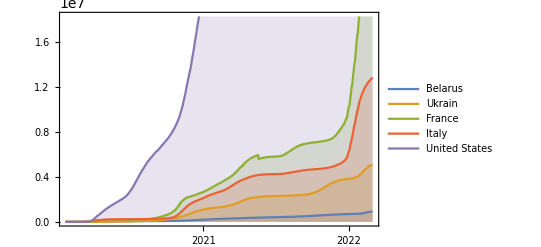

```mathematica
DateListPlot[{MapThread[{#1,#2}&,{dates,valuesBel}],MapThread[{#1,#2}&,{dates,valuesUkr}],MapThread[{#1,#2}&,{dates,valuesFr}],MapThread[{#1,#2}&,{dates,valuesIt}],MapThread[{#1,#2}&,{dates,valuesUS}]},Filling->Bottom,PlotLegends->{"Belarus","Ukrain","France","Italy","United States"}]
```